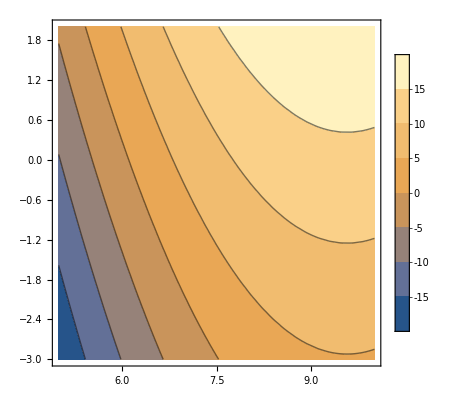

-Graphics-

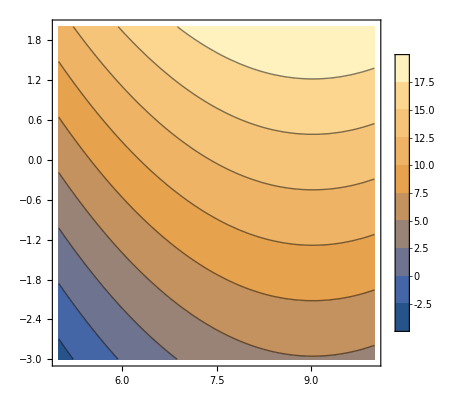

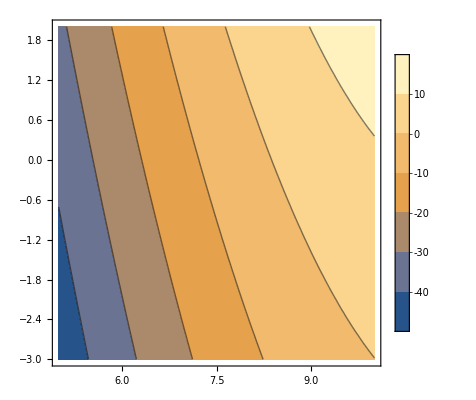

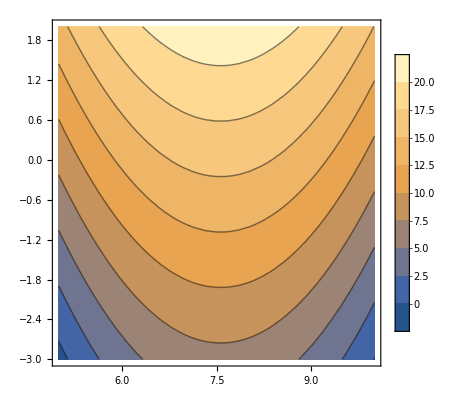

```mathematica
(* Log-normal mass function, today *)
LogNormalMassFunction[sigma_,Mstar_,M_]:=Exp[-(Log[M/Mstar])^2/(2sigma^2)]/(Sqrt[2Pi ] sigma M);
fPBH=10^-8;
gramsperGeV=1/(5.6095886 10^23);
pcpercm=3.086 10^18;
rhoDM=0.4 gramsperGeV pcpercm^3;
ContourPlot[Log10[LogNormalMassFunction[1.,10^10,10^M]rhoDM fPBH 4/3Pi (10^distance)^3],{M,5,10},{distance,-3,2},PlotLegends->Automatic]
ContourPlot[Log10[LogNormalMassFunction[1.,10^10,10^M]rhoDM fPBH 4/3Pi (10^distance)^3],{M,5,10},{distance,-3,2},PlotLegends->Automatic]
ContourPlot[Log10[LogNormalMassFunction[1.5,10^10,10^M]rhoDM fPBH 4/3Pi (10^distance)^3],{M,5,10},{distance,-3,2},PlotLegends->Automatic]
ContourPlot[Log10[LogNormalMassFunction[1.,10^12,10^M]rhoDM fPBH 4/3Pi (10^distance)^3],{M,5,10},{distance,-3,2},PlotLegends->Automatic]
ContourPlot[Log10[LogNormalMassFunction[1.,10^8,10^M]rhoDM fPBH 4/3Pi (10^distance)^3],{M,5,10},{distance,-3,2},PlotLegends->Automatic]
```

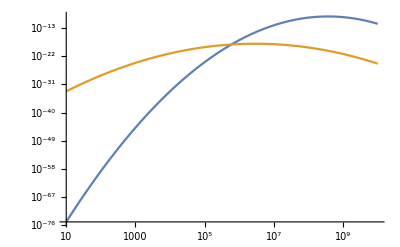

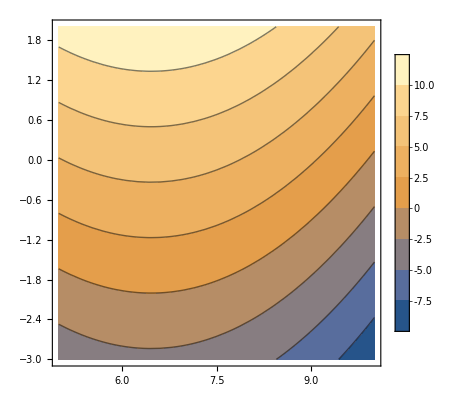

```mathematica
(* Now assume the mass function was at early times *)

(* this is the evaporation rate at late times, in grams/sec *)
alpha[mass_]:=4 10^-4 mass^2;

(* age of the universe *)
tU=14 10^9 365 24 60 60;

EvolvedMassFunction[sigma_,Mstar_,M_,time_]:=Exp[-(Log[(M^3+3.alpha[M] time)^(1/3)/Mstar])^2/(2sigma^2)]/(Sqrt[2Pi ] sigma (M^3+3.alpha[M] time)^(1/3))(M^3/((M^3+3.alpha[M] time)));

LogLogPlot[{LogNormalMassFunction[1.,10^9,M],EvolvedMassFunction[1.,10^9,M,tU]},{M,10^1,10^10}]

ContourPlot[Log10[EvolvedMassFunction[1.,10^9,10^M,tU]rhoDM fPBH 4/3Pi (10^distance)^3],{M,5,10},{distance,-3,2},PlotLegends->Automatic]
```